```mathematica
n=16
```

16

```mathematica
dfi=(2π)/n
```

π/8

```mathematica
p1=Table[{-0.49+0.01Cos[π-i dfi],0.01Sin[i dfi]},{i,0,n/4}];
```

```mathematica
p2=Table[{0.49+0.01Cos[π/2-i dfi],0.01Sin[π/2-i dfi]},{i,0,n/4}];
```

```mathematica
p3=Table[{-0.49+0.01Cos[π-i dfi],-0.01Sin[i dfi]},{i,0,n/4}];
```

```mathematica
p4=Table[{0.49+0.01Cos[π/2-i dfi],-0.01Sin[π/2-i dfi]},{i,0,n/4}];
```

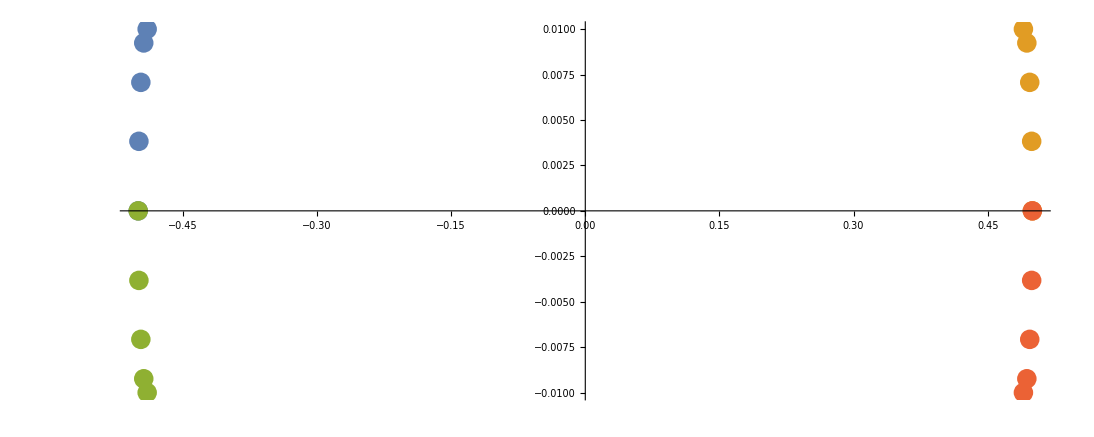

```mathematica
ListPlot[{p1,p2,p3,p4},AspectRatio->Automatic]
```

```mathematica
Join[p1,p2]
```

{{-0.5,0.},{-0.499239,0.00382683},{-0.497071,0.00707107},{-0.493827,0.0092388},{-0.49,0.01},{0.49,0.01},{0.493827,0.0092388},{0.497071,0.00707107},{0.499239,0.00382683},{0.5,0.}}

```mathematica
data=Flatten[{"aaa","bbb",Length[p1]+Length[p2]-1,Length[p3]+Length[p4]-1,"up",Join[p1,p2],"down",Join[p3,p4]},1]
```

{aaa,bbb,9,9,up,{-0.5,0.},{-0.499239,0.00382683},{-0.497071,0.00707107},{-0.493827,0.0092388},{-0.49,0.01},{0.49,0.01},{0.493827,0.0092388},{0.497071,0.00707107},{0.499239,0.00382683},{0.5,0.},down,{-0.5,0.},{-0.499239,-0.00382683},{-0.497071,-0.00707107},{-0.493827,-0.0092388},{-0.49,-0.01},{0.49,-0.01},{0.493827,-0.0092388},{0.497071,-0.00707107},{0.499239,-0.00382683},{0.5,0.}}

```mathematica
p1Rev=Reverse[p1]
```

{{-0.49,0.01},{-0.493827,0.0092388},{-0.497071,0.00707107},{-0.499239,0.00382683},{-0.5,0.}}

```mathematica
p2Rev=Reverse@p2
```

{{0.5,0.},{0.499239,0.00382683},{0.497071,0.00707107},{0.493827,0.0092388},{0.49,0.01}}

```mathematica
p12=Table[{0.49,0.01}+({-0.49,0.01}-{0.49,0.01})/256 i,{i,1,255}]
```

{{0.486172,0.01},{0.482344,0.01},{0.478516,0.01},{0.474688,0.01},{0.470859,0.01},{0.467031,0.01},{0.463203,0.01},{0.459375,0.01},{0.455547,0.01},{0.451719,0.01},{0.447891,0.01},{0.444062,0.01},{0.440234,0.01},{0.436406,0.01},{0.432578,0.01},{0.42875,0.01},{0.424922,0.01},{0.421094,0.01},{0.417266,0.01},{0.413438,0.01},{0.409609,0.01},{0.405781,0.01},{0.401953,0.01},{0.398125,0.01},{0.394297,0.01},{0.390469,0.01},{0.386641,0.01},{0.382813,0.01},{0.378984,0.01},{0.375156,0.01},{0.371328,0.01},{0.3675,0.01},{0.363672,0.01},{0.359844,0.01},{0.356016,0.01},{0.352188,0.01},{0.348359,0.01},{0.344531,0.01},{0.340703,0.01},{0.336875,0.01},{0.333047,0.01},{0.329219,0.01},{0.325391,0.01},{0.321563,0.01},{0.317734,0.01},{0.313906,0.01},{0.310078,0.01},{0.30625,0.01},{0.302422,0.01},{0.298594,0.01},{0.294766,0.01},{0.290937,0.01},{0.287109,0.01},{0.283281,0.01},{0.279453,0.01},{0.275625,0.01},{0.271797,0.01},{0.267969,0.01},{0.264141,0.01},{0.260313,0.01},{0.256484,0.01},{0.252656,0.01},{0.248828,0.01},{0.245,0.01},{0.241172,0.01},{0.237344,0.01},{0.233516,0.01},{0.229688,0.01},{0.225859,0.01},{0.222031,0.01},{0.218203,0.01},{0.214375,0.01},{0.210547,0.01},{0.206719,0.01},{0.202891,0.01},{0.199062,0.01},{0.195234,0.01},{0.191406,0.01},{0.187578,0.01},{0.18375,0.01},{0.179922,0.01},{0.176094,0.01},{0.172266,0.01},{0.168438,0.01},{0.164609,0.01},{0.160781,0.01},{0.156953,0.01},{0.153125,0.01},{0.149297,0.01},{0.145469,0.01},{0.141641,0.01},{0.137813,0.01},{0.133984,0.01},{0.130156,0.01},{0.126328,0.01},{0.1225,0.01},{0.118672,0.01},{0.114844,0.01},{0.111016,0.01},{0.107187,0.01},{0.103359,0.01},{0.0995313,0.01},{0.0957031,0.01},{0.091875,0.01},{0.0880469,0.01},{0.0842188,0.01},{0.0803906,0.01},{0.0765625,0.01},{0.0727344,0.01},{0.0689063,0.01},{0.0650781,0.01},{0.06125,0.01},{0.0574219,0.01},{0.0535937,0.01},{0.0497656,0.01},{0.0459375,0.01},{0.0421094,0.01},{0.0382812,0.01},{0.0344531,0.01},{0.030625,0.01},{0.0267969,0.01},{0.0229687,0.01},{0.0191406,0.01},{0.0153125,0.01},{0.0114844,0.01},{0.00765625,0.01},{0.00382813,0.01},{0.,0.01},{-0.00382813,0.01},{-0.00765625,0.01},{-0.0114844,0.01},{-0.0153125,0.01},{-0.0191406,0.01},{-0.0229687,0.01},{-0.0267969,0.01},{-0.030625,0.01},{-0.0344531,0.01},{-0.0382813,0.01},{-0.0421094,0.01},{-0.0459375,0.01},{-0.0497656,0.01},{-0.0535937,0.01},{-0.0574219,0.01},{-0.06125,0.01},{-0.0650781,0.01},{-0.0689062,0.01},{-0.0727344,0.01},{-0.0765625,0.01},{-0.0803906,0.01},{-0.0842188,0.01},{-0.0880469,0.01},{-0.091875,0.01},{-0.0957031,0.01},{-0.0995312,0.01},{-0.103359,0.01},{-0.107187,0.01},{-0.111016,0.01},{-0.114844,0.01},{-0.118672,0.01},{-0.1225,0.01},{-0.126328,0.01},{-0.130156,0.01},{-0.133984,0.01},{-0.137813,0.01},{-0.141641,0.01},{-0.145469,0.01},{-0.149297,0.01},{-0.153125,0.01},{-0.156953,0.01},{-0.160781,0.01},{-0.164609,0.01},{-0.168438,0.01},{-0.172266,0.01},{-0.176094,0.01},{-0.179922,0.01},{-0.18375,0.01},{-0.187578,0.01},{-0.191406,0.01},{-0.195234,0.01},{-0.199063,0.01},{-0.202891,0.01},{-0.206719,0.01},{-0.210547,0.01},{-0.214375,0.01},{-0.218203,0.01},{-0.222031,0.01},{-0.225859,0.01},{-0.229688,0.01},{-0.233516,0.01},{-0.237344,0.01},{-0.241172,0.01},{-0.245,0.01},{-0.248828,0.01},{-0.252656,0.01},{-0.256484,0.01},{-0.260312,0.01},{-0.264141,0.01},{-0.267969,0.01},{-0.271797,0.01},{-0.275625,0.01},{-0.279453,0.01},{-0.283281,0.01},{-0.287109,0.01},{-0.290937,0.01},{-0.294766,0.01},{-0.298594,0.01},{-0.302422,0.01},{-0.30625,0.01},{-0.310078,0.01},{-0.313906,0.01},{-0.317734,0.01},{-0.321563,0.01},{-0.325391,0.01},{-0.329219,0.01},{-0.333047,0.01},{-0.336875,0.01},{-0.340703,0.01},{-0.344531,0.01},{-0.348359,0.01},{-0.352188,0.01},{-0.356016,0.01},{-0.359844,0.01},{-0.363672,0.01},{-0.3675,0.01},{-0.371328,0.01},{-0.375156,0.01},{-0.378984,0.01},{-0.382813,0.01},{-0.386641,0.01},{-0.390469,0.01},{-0.394297,0.01},{-0.398125,0.01},{-0.401953,0.01},{-0.405781,0.01},{-0.409609,0.01},{-0.413438,0.01},{-0.417266,0.01},{-0.421094,0.01},{-0.424922,0.01},{-0.42875,0.01},{-0.432578,0.01},{-0.436406,0.01},{-0.440234,0.01},{-0.444063,0.01},{-0.447891,0.01},{-0.451719,0.01},{-0.455547,0.01},{-0.459375,0.01},{-0.463203,0.01},{-0.467031,0.01},{-0.470859,0.01},{-0.474688,0.01},{-0.478516,0.01},{-0.482344,0.01},{-0.486172,0.01}}

```mathematica
p3Rev=p3
```

{{-0.5,0.},{-0.499239,-0.00382683},{-0.497071,-0.00707107},{-0.493827,-0.0092388},{-0.49,-0.01}}

```mathematica
p4Rev=p4
```

{{0.49,-0.01},{0.493827,-0.0092388},{0.497071,-0.00707107},{0.499239,-0.00382683},{0.5,0.}}

```mathematica
p34=Table[{-0.49,-0.01}+({0.49,-0.01}-{-0.49,-0.01})/256 i,{i,1,255}];
```

```mathematica
p2Rev
```

{{0.5,0.},{0.499239,0.00382683},{0.497071,0.00707107},{0.493827,0.0092388},{0.49,0.01}}

```mathematica
p12
```

{{0.486172,0.01},{0.482344,0.01},{0.478516,0.01},{0.474688,0.01},{0.470859,0.01},{0.467031,0.01},{0.463203,0.01},{0.459375,0.01},{0.455547,0.01},{0.451719,0.01},{0.447891,0.01},{0.444062,0.01},{0.440234,0.01},{0.436406,0.01},{0.432578,0.01},{0.42875,0.01},{0.424922,0.01},{0.421094,0.01},{0.417266,0.01},{0.413438,0.01},{0.409609,0.01},{0.405781,0.01},{0.401953,0.01},{0.398125,0.01},{0.394297,0.01},{0.390469,0.01},{0.386641,0.01},{0.382813,0.01},{0.378984,0.01},{0.375156,0.01},{0.371328,0.01},{0.3675,0.01},{0.363672,0.01},{0.359844,0.01},{0.356016,0.01},{0.352188,0.01},{0.348359,0.01},{0.344531,0.01},{0.340703,0.01},{0.336875,0.01},{0.333047,0.01},{0.329219,0.01},{0.325391,0.01},{0.321563,0.01},{0.317734,0.01},{0.313906,0.01},{0.310078,0.01},{0.30625,0.01},{0.302422,0.01},{0.298594,0.01},{0.294766,0.01},{0.290937,0.01},{0.287109,0.01},{0.283281,0.01},{0.279453,0.01},{0.275625,0.01},{0.271797,0.01},{0.267969,0.01},{0.264141,0.01},{0.260313,0.01},{0.256484,0.01},{0.252656,0.01},{0.248828,0.01},{0.245,0.01},{0.241172,0.01},{0.237344,0.01},{0.233516,0.01},{0.229688,0.01},{0.225859,0.01},{0.222031,0.01},{0.218203,0.01},{0.214375,0.01},{0.210547,0.01},{0.206719,0.01},{0.202891,0.01},{0.199062,0.01},{0.195234,0.01},{0.191406,0.01},{0.187578,0.01},{0.18375,0.01},{0.179922,0.01},{0.176094,0.01},{0.172266,0.01},{0.168438,0.01},{0.164609,0.01},{0.160781,0.01},{0.156953,0.01},{0.153125,0.01},{0.149297,0.01},{0.145469,0.01},{0.141641,0.01},{0.137813,0.01},{0.133984,0.01},{0.130156,0.01},{0.126328,0.01},{0.1225,0.01},{0.118672,0.01},{0.114844,0.01},{0.111016,0.01},{0.107187,0.01},{0.103359,0.01},{0.0995313,0.01},{0.0957031,0.01},{0.091875,0.01},{0.0880469,0.01},{0.0842188,0.01},{0.0803906,0.01},{0.0765625,0.01},{0.0727344,0.01},{0.0689063,0.01},{0.0650781,0.01},{0.06125,0.01},{0.0574219,0.01},{0.0535937,0.01},{0.0497656,0.01},{0.0459375,0.01},{0.0421094,0.01},{0.0382812,0.01},{0.0344531,0.01},{0.030625,0.01},{0.0267969,0.01},{0.0229687,0.01},{0.0191406,0.01},{0.0153125,0.01},{0.0114844,0.01},{0.00765625,0.01},{0.00382813,0.01},{0.,0.01},{-0.00382813,0.01},{-0.00765625,0.01},{-0.0114844,0.01},{-0.0153125,0.01},{-0.0191406,0.01},{-0.0229687,0.01},{-0.0267969,0.01},{-0.030625,0.01},{-0.0344531,0.01},{-0.0382813,0.01},{-0.0421094,0.01},{-0.0459375,0.01},{-0.0497656,0.01},{-0.0535937,0.01},{-0.0574219,0.01},{-0.06125,0.01},{-0.0650781,0.01},{-0.0689062,0.01},{-0.0727344,0.01},{-0.0765625,0.01},{-0.0803906,0.01},{-0.0842188,0.01},{-0.0880469,0.01},{-0.091875,0.01},{-0.0957031,0.01},{-0.0995312,0.01},{-0.103359,0.01},{-0.107187,0.01},{-0.111016,0.01},{-0.114844,0.01},{-0.118672,0.01},{-0.1225,0.01},{-0.126328,0.01},{-0.130156,0.01},{-0.133984,0.01},{-0.137813,0.01},{-0.141641,0.01},{-0.145469,0.01},{-0.149297,0.01},{-0.153125,0.01},{-0.156953,0.01},{-0.160781,0.01},{-0.164609,0.01},{-0.168438,0.01},{-0.172266,0.01},{-0.176094,0.01},{-0.179922,0.01},{-0.18375,0.01},{-0.187578,0.01},{-0.191406,0.01},{-0.195234,0.01},{-0.199063,0.01},{-0.202891,0.01},{-0.206719,0.01},{-0.210547,0.01},{-0.214375,0.01},{-0.218203,0.01},{-0.222031,0.01},{-0.225859,0.01},{-0.229688,0.01},{-0.233516,0.01},{-0.237344,0.01},{-0.241172,0.01},{-0.245,0.01},{-0.248828,0.01},{-0.252656,0.01},{-0.256484,0.01},{-0.260312,0.01},{-0.264141,0.01},{-0.267969,0.01},{-0.271797,0.01},{-0.275625,0.01},{-0.279453,0.01},{-0.283281,0.01},{-0.287109,0.01},{-0.290937,0.01},{-0.294766,0.01},{-0.298594,0.01},{-0.302422,0.01},{-0.30625,0.01},{-0.310078,0.01},{-0.313906,0.01},{-0.317734,0.01},{-0.321563,0.01},{-0.325391,0.01},{-0.329219,0.01},{-0.333047,0.01},{-0.336875,0.01},{-0.340703,0.01},{-0.344531,0.01},{-0.348359,0.01},{-0.352188,0.01},{-0.356016,0.01},{-0.359844,0.01},{-0.363672,0.01},{-0.3675,0.01},{-0.371328,0.01},{-0.375156,0.01},{-0.378984,0.01},{-0.382813,0.01},{-0.386641,0.01},{-0.390469,0.01},{-0.394297,0.01},{-0.398125,0.01},{-0.401953,0.01},{-0.405781,0.01},{-0.409609,0.01},{-0.413438,0.01},{-0.417266,0.01},{-0.421094,0.01},{-0.424922,0.01},{-0.42875,0.01},{-0.432578,0.01},{-0.436406,0.01},{-0.440234,0.01},{-0.444063,0.01},{-0.447891,0.01},{-0.451719,0.01},{-0.455547,0.01},{-0.459375,0.01},{-0.463203,0.01},{-0.467031,0.01},{-0.470859,0.01},{-0.474688,0.01},{-0.478516,0.01},{-0.482344,0.01},{-0.486172,0.01}}

```mathematica
p1Rev
```

{{-0.49,0.01},{-0.493827,0.0092388},{-0.497071,0.00707107},{-0.499239,0.00382683},{-0.5,0.}}

```mathematica
p3[[2;;]]
```

{{-0.499239,-0.00382683},{-0.497071,-0.00707107},{-0.493827,-0.0092388},{-0.49,-0.01}}

```mathematica
p34
```

{{-0.486172,-0.01},{-0.482344,-0.01},{-0.478516,-0.01},{-0.474688,-0.01},{-0.470859,-0.01},{-0.467031,-0.01},{-0.463203,-0.01},{-0.459375,-0.01},{-0.455547,-0.01},{-0.451719,-0.01},{-0.447891,-0.01},{-0.444062,-0.01},{-0.440234,-0.01},{-0.436406,-0.01},{-0.432578,-0.01},{-0.42875,-0.01},{-0.424922,-0.01},{-0.421094,-0.01},{-0.417266,-0.01},{-0.413438,-0.01},{-0.409609,-0.01},{-0.405781,-0.01},{-0.401953,-0.01},{-0.398125,-0.01},{-0.394297,-0.01},{-0.390469,-0.01},{-0.386641,-0.01},{-0.382813,-0.01},{-0.378984,-0.01},{-0.375156,-0.01},{-0.371328,-0.01},{-0.3675,-0.01},{-0.363672,-0.01},{-0.359844,-0.01},{-0.356016,-0.01},{-0.352188,-0.01},{-0.348359,-0.01},{-0.344531,-0.01},{-0.340703,-0.01},{-0.336875,-0.01},{-0.333047,-0.01},{-0.329219,-0.01},{-0.325391,-0.01},{-0.321563,-0.01},{-0.317734,-0.01},{-0.313906,-0.01},{-0.310078,-0.01},{-0.30625,-0.01},{-0.302422,-0.01},{-0.298594,-0.01},{-0.294766,-0.01},{-0.290937,-0.01},{-0.287109,-0.01},{-0.283281,-0.01},{-0.279453,-0.01},{-0.275625,-0.01},{-0.271797,-0.01},{-0.267969,-0.01},{-0.264141,-0.01},{-0.260313,-0.01},{-0.256484,-0.01},{-0.252656,-0.01},{-0.248828,-0.01},{-0.245,-0.01},{-0.241172,-0.01},{-0.237344,-0.01},{-0.233516,-0.01},{-0.229688,-0.01},{-0.225859,-0.01},{-0.222031,-0.01},{-0.218203,-0.01},{-0.214375,-0.01},{-0.210547,-0.01},{-0.206719,-0.01},{-0.202891,-0.01},{-0.199062,-0.01},{-0.195234,-0.01},{-0.191406,-0.01},{-0.187578,-0.01},{-0.18375,-0.01},{-0.179922,-0.01},{-0.176094,-0.01},{-0.172266,-0.01},{-0.168438,-0.01},{-0.164609,-0.01},{-0.160781,-0.01},{-0.156953,-0.01},{-0.153125,-0.01},{-0.149297,-0.01},{-0.145469,-0.01},{-0.141641,-0.01},{-0.137813,-0.01},{-0.133984,-0.01},{-0.130156,-0.01},{-0.126328,-0.01},{-0.1225,-0.01},{-0.118672,-0.01},{-0.114844,-0.01},{-0.111016,-0.01},{-0.107187,-0.01},{-0.103359,-0.01},{-0.0995313,-0.01},{-0.0957031,-0.01},{-0.091875,-0.01},{-0.0880469,-0.01},{-0.0842188,-0.01},{-0.0803906,-0.01},{-0.0765625,-0.01},{-0.0727344,-0.01},{-0.0689063,-0.01},{-0.0650781,-0.01},{-0.06125,-0.01},{-0.0574219,-0.01},{-0.0535937,-0.01},{-0.0497656,-0.01},{-0.0459375,-0.01},{-0.0421094,-0.01},{-0.0382812,-0.01},{-0.0344531,-0.01},{-0.030625,-0.01},{-0.0267969,-0.01},{-0.0229687,-0.01},{-0.0191406,-0.01},{-0.0153125,-0.01},{-0.0114844,-0.01},{-0.00765625,-0.01},{-0.00382813,-0.01},{0.,-0.01},{0.00382813,-0.01},{0.00765625,-0.01},{0.0114844,-0.01},{0.0153125,-0.01},{0.0191406,-0.01},{0.0229687,-0.01},{0.0267969,-0.01},{0.030625,-0.01},{0.0344531,-0.01},{0.0382813,-0.01},{0.0421094,-0.01},{0.0459375,-0.01},{0.0497656,-0.01},{0.0535937,-0.01},{0.0574219,-0.01},{0.06125,-0.01},{0.0650781,-0.01},{0.0689062,-0.01},{0.0727344,-0.01},{0.0765625,-0.01},{0.0803906,-0.01},{0.0842188,-0.01},{0.0880469,-0.01},{0.091875,-0.01},{0.0957031,-0.01},{0.0995312,-0.01},{0.103359,-0.01},{0.107187,-0.01},{0.111016,-0.01},{0.114844,-0.01},{0.118672,-0.01},{0.1225,-0.01},{0.126328,-0.01},{0.130156,-0.01},{0.133984,-0.01},{0.137813,-0.01},{0.141641,-0.01},{0.145469,-0.01},{0.149297,-0.01},{0.153125,-0.01},{0.156953,-0.01},{0.160781,-0.01},{0.164609,-0.01},{0.168438,-0.01},{0.172266,-0.01},{0.176094,-0.01},{0.179922,-0.01},{0.18375,-0.01},{0.187578,-0.01},{0.191406,-0.01},{0.195234,-0.01},{0.199063,-0.01},{0.202891,-0.01},{0.206719,-0.01},{0.210547,-0.01},{0.214375,-0.01},{0.218203,-0.01},{0.222031,-0.01},{0.225859,-0.01},{0.229688,-0.01},{0.233516,-0.01},{0.237344,-0.01},{0.241172,-0.01},{0.245,-0.01},{0.248828,-0.01},{0.252656,-0.01},{0.256484,-0.01},{0.260312,-0.01},{0.264141,-0.01},{0.267969,-0.01},{0.271797,-0.01},{0.275625,-0.01},{0.279453,-0.01},{0.283281,-0.01},{0.287109,-0.01},{0.290937,-0.01},{0.294766,-0.01},{0.298594,-0.01},{0.302422,-0.01},{0.30625,-0.01},{0.310078,-0.01},{0.313906,-0.01},{0.317734,-0.01},{0.321563,-0.01},{0.325391,-0.01},{0.329219,-0.01},{0.333047,-0.01},{0.336875,-0.01},{0.340703,-0.01},{0.344531,-0.01},{0.348359,-0.01},{0.352188,-0.01},{0.356016,-0.01},{0.359844,-0.01},{0.363672,-0.01},{0.3675,-0.01},{0.371328,-0.01},{0.375156,-0.01},{0.378984,-0.01},{0.382813,-0.01},{0.386641,-0.01},{0.390469,-0.01},{0.394297,-0.01},{0.398125,-0.01},{0.401953,-0.01},{0.405781,-0.01},{0.409609,-0.01},{0.413438,-0.01},{0.417266,-0.01},{0.421094,-0.01},{0.424922,-0.01},{0.42875,-0.01},{0.432578,-0.01},{0.436406,-0.01},{0.440234,-0.01},{0.444063,-0.01},{0.447891,-0.01},{0.451719,-0.01},{0.455547,-0.01},{0.459375,-0.01},{0.463203,-0.01},{0.467031,-0.01},{0.470859,-0.01},{0.474688,-0.01},{0.478516,-0.01},{0.482344,-0.01},{0.486172,-0.01}}

```mathematica
p4[[;;-2]]
```

{{0.49,-0.01},{0.493827,-0.0092388},{0.497071,-0.00707107},{0.499239,-0.00382683}}

```mathematica
allPoints=p2Rev~Join~p12~Join~p1Rev~Join~p3[[2;;]]~Join~p34~Join~p4[[;;-2]];
```

```mathematica
allPoints[[-1]]
```

{0.499239,-0.00382683}

```mathematica
Manipulate[ListLinePlot[allPoints[[1;;j]]],{j,1,528,1}]
```

Part::take: Cannot take positions 1 through 1 in allPoints.

ListLinePlot::lpn: allPoints⟦1;;1⟧ is not a list of numbers or pairs of numbers.

```mathematica
Length[allPoints]
```

528

```mathematica
len=Norm[#]&/@(RotateLeft[allPoints]-allPoints);
```

```mathematica
Length[len]
```

528

```mathematica
kas=Normalize[#]&/@(RotateLeft[allPoints]-allPoints);
```

```mathematica
nrm={#[[2]],-#[[1]]}&/@kas;
```

```mathematica
allParam=Table[
Flatten[{i-1,
allPoints[[i]][[1]],allPoints[[i,2]],(*начало панели*)
RotateLeft[allPoints][[i]][[1]],RotateLeft[allPoints][[i,2]],(*конец панели*) 
((allPoints[[i]]+RotateLeft[allPoints][[i]])/2)[[1]],((allPoints[[i]]+RotateLeft[allPoints][[i]])/2)[[2]], (*контрольная точка ??????*)
allPoints[[i]][[1]],allPoints[[i,2]], (*точка рождения вихря ??????*)
nrm[[i]][[1]],nrm[[i]][[2]],
kas[[i]][[1]],kas[[i]][[2]],
len[[i]],
If[i>1,i-2,Length[len]-1],
If[i-1<Length[len]-1,i,0]},1]
,{i,1,Length@allPoints}
]
```

{{0,0.5,0.,0.499239,0.00382683,0.499619,0.00191342,0.5,0.,0.980785,0.19509,-0.19509,0.980785,0.00390181,527,1},526,{527,0.499239,-0.00382683,0.5,0.,0.499619,-0.00191342,2,0.980785,-0.19509,0.19509,0.980785,0.00390181,526,0}}
 |  |  |  |

```mathematica
MinMax[allParam[[All,-3]]]
```

{0.00382812,0.00390181}

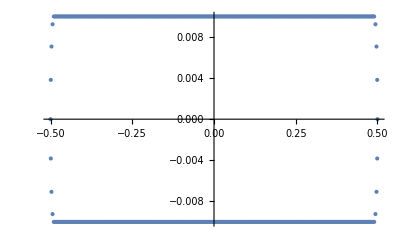

```mathematica
ListPlot[allPoints]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Git\VM2D\build\Airfoils\Generators\Blasius

```mathematica
Export["blas200Rev.pfl",dataRev,"Table"]
```

blas200Rev.pfl

```mathematica
toExport={{"xxx"},{"xxx"},{Length[allParam]}}~Join~allParam~Join~{{"xxx"},{"0"},{"xxx"},{"0"},{"xxx"},{-0.5, -0.01, 0.5, 0.01}};
```

```mathematica
Export["blas200Rev",toExport,"Table"]
```

blas200Rev.txt

```mathematica
allParam[[1]]
```

{0,0.5,0.,0.499239,0.00382683,0.499619,0.00191342,0.5,0.,0.980785,0.19509,-0.19509,0.980785,0.00390181,527,1}